Last modified on: Wednesday, July 11, 2018 at 2:02

Author Info

Milad Pourrahmani

Carlo Barbieri

University of California, Irvine

Poster Session Content

A New Kind of Chess

The rules of chess have been perfected for more than a millennia to ensure an exciting game every time. These relatively simple rules are capable of producing very interesting and complex dynamics that deserve to be studied in their own rights, not just merely for competition purposes. This project aims at laying down the formalism to capture the game of chess as well as many other board and card games. In accordance with this formalism, a Mathematica chess package has been developed which creates, displays, and evolves a ChessState object using ChessState, ChessPlot, and ChessEvolve functions.

Add the most representative image of your project here. (We recommend just 1 image, if you add more, we will make a collage of the images.)

-Graphics-

ChessPlot enables the user to provide options such as board color set, display coordinates, rotate point of view, or extract MatrixForm of a ChessState. In addition,  a list of rule functions is provided which take in a ChessState and output all the possible moves in accordance with the rule they represent.

With this setup, the user is able to setup any ChessEvaluate function and explore the chess space. This open-ended chess design also enables the user to modify the rules with ease so they can explore chess variations such as antichess, atomic chess, and others.

Note: Everything above this bar is your poster.Make sure it fits on a single page. "Preview Poster"

End of School Presentation Content

In addition to the poster content, include other content to present at the 2 minute presentation for end of school. Use the buttons below to add more sections."Add Header""Add Text""Add Code or Image"

ChessState

-Graphics-

ChessState[-Graphics-]

ChessPlot

ChessPlot[ChessState[-Graphics-], "WhiteOrientation" → "Left",  "ShowCoordinates" → True, "BoardColorSet" → {LightRed, Pink}, ImageSize → 375]

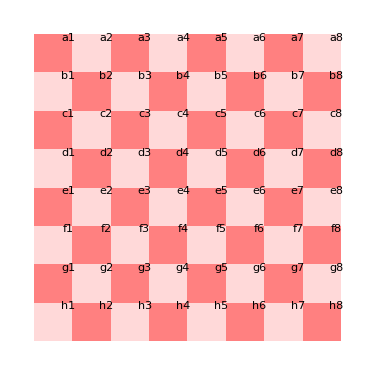

Chess Rules   → Possible Moves Generators
Chess Moves → A Set of Actions

Example:
Any ♘ may move from pos_1 to pos_2 = pos_1 + ∀{{±1, ±2}, {±2, ±1}} if S(pos_2)== ∀{♛, ♜, ♝, ♞, ♟, □}.

possibleMoves = KnightMoves[ChessState[-Graphics-]]
{{b8→□,a6→♞},{b8→□,c6→♞},{g8→□,f6→♞},{g8 → □, h6 → ♞}}

ChessEvolve

ChessEvolve[ChessState[-Graphics-],possibleMoves]

Note: Everything above this bar is in your 2 minute presentation. Make sure it fits on 2 slides. "Preview Presentation"

Detailed Project Notes

#### Main Results in Detail

A board/card game can be represented using an association where coordinates in the game are associated to states.
Specifically for chess, we can write:

<|
"a8"→"♜","b8"→"♞","c8"→"♝","d8"→"♛","e8"→"♚","f8"→"♝","g8"→"♞","h8"→"♜","a7"→"♟","b7"→"♟","c7"→"♟","d7"→"♟","e7"→"♟","f7"→"♟","g7"→"♟","h7"→"♟","a6"→"□","b6"→"□","c6"→"□","d6"→"□","e6"→"□","f6"→"□","g6"→"□","h6"→"□","a5"→"□","b5"→"□","c5"→"□","d5"→"□","e5"→"□","f5"→"□","g5"→"□","h5"→"□","a4"→"□","b4"→"□","c4"→"□","d4"→"□","e4"→"□","f4"→"□","g4"→"□","h4"→"□","a3"→"□","b3"→"□","c3"→"□","d3"→"□","e3"→"□","f3"→"□","g3"→"□","h3"→"□","a2"→"♙","b2"→"♙","c2"→"♙","d2"→"♙","e2"→"♙","f2"→"♙","g2"→"♙","h2"→"♙","a1"→"♖","b1"→"♘","c1"→"♗","d1"→"♕","e1"→"♔","f1"→"♗","g1"→"♘","h1"→"♖","♖♔"→True,"♔♖"→True,"♜♚"→True,"♚♜"→True,"EnPassant"→None,"WhiteCemetery"→{},"BlackCemetery"→{},"Turn"→"White","Result"→None
|>

In order to avoid referring to previous states of the game, auxiliary (as in not part of the board) has been added. For instance, if a pawn may be captured via En passant, it’s coordinate will be mentioned. As another example, if the rooks or the king move, the opportunity of castling will be revoked. White and black cemeteries are there to keep track of captured pieces. Turn switches between White and Black after each move. The game ends when the Result is set to “1/2-1/2”, “1-0”, or “0-1”.

A move is a list of actions. For instance, the move of a white pawn at a7 capturing a rook at b8 and becoming a queen may be represented as {a7 → □, ♜→ BlackCemetery,  b8 → ♕}. 

In order to explore the game space, the rules of the game may be translated to functions which intake a state of a game and output a list of all possible moves.

To construct these function for chess, I have expressed the rules mathematically:

pos_1= {rank, file} represents the matrix coordinate in current player’s frame of reference
When a piece legally moves to an occupied square by the opponent, the opponents piece is captures.
Captured pieces go to their corresponding cemetery.
† is a hyperstate of a square that is under attack by opponents pieces. That is, in the current state, the opponent has a move that ∀{♔, ♕, ♖, ♗, ♘, ♙} → WhiteCemetery.
If S(pos_♔) == † with no legal moves, the result is set to “0-1” and game ends.
If S(pos_♔) ≠ † with no legal moves, the game ends as “1/2-1/2”.


A. □
	1. No possible moves from it.
B. ♔ KingRestrictoins
	1. Eliminate all moves that result in S(pos_♔) == †.
C. ♙ PawnMoves
	1. May move to pos_2 = pos_1 + {1, 0} if S(pos_2)== □ & pos_2 < {8, ∀}
	2. May move to pos_2 = pos_1 + {0, +2} if pos_1 == {∀, 2} & S(pos_2 + {0, -1} )== □ & S(pos_2)== □.
	3. May move to pos_2 = pos_1 + ∀{{1, 0}, {±1, +1}} as ∀{♕, ♖, ♗, ♘} if pos_2 == {8, ∀} & S(pos_2)== {♛, ♜, ♝, ♞, ♟, □}.
	5. May move to pos_2= pos_1 + ∀{{±1, +1}} if S_-1(pos_2) == ♟ & S(pos_2 - {0, 2}) == ♟ and capture pos_2 - {0, 2}.
D. ♘ KnightMoves
	1. May move to pos_2 = pos_1 + ∀{{±1, ±2}, {±2, ±1}} if S(pos_2)== ∀{♛, ♜, ♝, ♞, ♟, □}.
E. ♗ BishopMoves
	1. For dir= ∀{±1, ±1} and n = ∀{1, ..., 8-1}, may move to pos = pos_0 + n ×dir if S(pos)== ∀{♛, ♜, ♝, ♞, ♟, □} and  S(pos_0 + {1, ..., n-1}dir) == □.
F. ♖ RookMoves
	1. For dir= ∀{{±1, 0}, {0, ±1}} and n = ∀{1, ..., 8-1}, may move to pos = pos_0 + n ×dir if S(pos)== ∀{♛, ♜, ♝, ♞, ♟, □} and  S(pos_0 + {1, ..., n-1}dir) == □.
G. ♕ QueenMoves
	1. For dir= ∀{{±1, 0}, {0, ±1}, {±1, ±1}} and n = ∀{1, ..., 8-1}, may move to pos = pos_0 + n ×dir if S(pos)== ∀{♛, ♜, ♝, ♞, ♟, □} and  S(pos_0 + {1, ..., n-1}dir) == □.
H. ♔ KingMoves
	1. For dir= ∀{{±1, 0}, {0, ±1}, {±1, ±1}}, may move to pos_2 = pos_1 + dir if S(pos_2)== ∀{♛, ♜, ♝, ♞, ♟, □}. 
	2. May {e1 → □, h1 → □, f1 → ♖, g1 → ♔} if f1 & g1 == □ & S(e1) ≠ † & S_i(e1) == ♔ for all i < t & S_i(h1) == ♖ for all i < t.
	3. May {e1 → □, a1 → □, d1 → ♖, c1 → ♔} if b1, c1, d1 == □ & S("e1") ≠ † & S_i("e1") == ♔ for all i < t & S_i("a1") == ♖ for all i < t.

Similarly for black.

#### Code

You can import chess.m as a package or use Notebook01.nb for code, documentation, and demonstration

https://github.com/Miladiouss/Summer2018Starter/tree/master/ChessPackage

#### Keywords

Chess

Antichess

Atomic Chess

Open-ended Chess

Chess Algorithm

Chess in Mathematica

Mathematical representation of chess rules

#### Other information